```mathematica
(*Mathematica*)
```

-1+61 x^3-215 x^6-61 x^9-x^12

{{-0.900654,0.,-0.434537},{-0.486258,0.,-0.873815},{-0.450327,-0.779989,0.434537},{-0.450327,0.779989,0.434537},{-0.243129,-0.421112,0.873815},{-0.243129,0.421112,0.873815},{0.243129,-0.421112,-0.873815},{0.243129,0.421112,-0.873815},{0.450327,-0.779989,-0.434537},{0.450327,0.779989,-0.434537},{0.486258,0.,0.873815},{0.900654,0.,0.434537}}

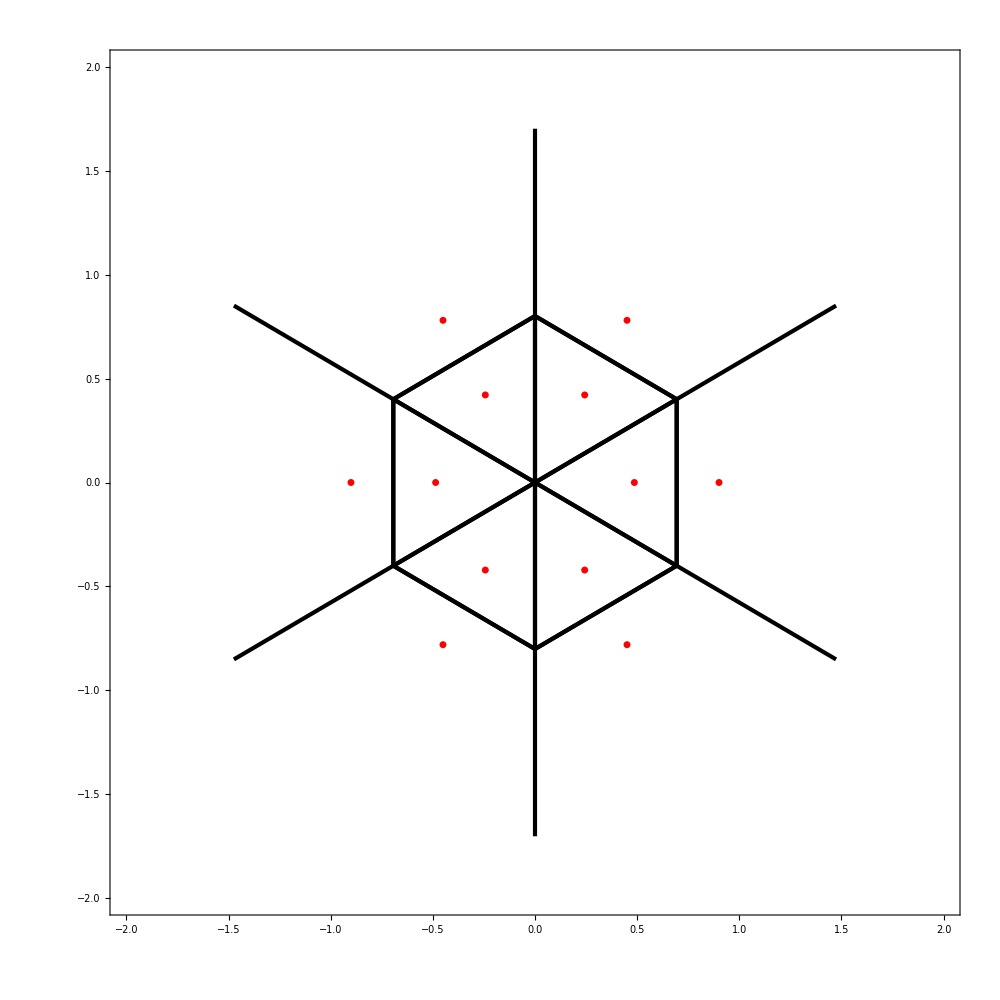

-Graphics3D-

20

```mathematica
<<ComputationalGeometry`
pa[x_]=-1+61 x^3-215 x^6-61 x^9-x^12
pts=Union[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pa[x]==0,x]]
ptsn=Table[Hue[Norm[x/.NSolve[pa[x]==0,x][[i]]]],{i,Length[pts]}];
(* Voronoi diagram*)
g1=Show[{
DiagramPlot[Most/@pts,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[Most/@pts]}]
},PlotRange->{{-2,2},{-2,2}},Frame->True,PlotRangeClipping->True,ImageSize->1000]
(* 3d projection of polyhedron*)
Show[Graphics3D[{Red,PointSize[0.0375],Point/@pts}],Axes->True]
(* convex hull: MathWorld Library*)
<<ConvexHull`
hull0=ConvexHull3D[pts];
Length[hull0]
hull1=Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{Hue[1],hull0[[i]]}],{i,Length[hull0]}]];
```

```mathematica
g=Graphics3D[hull={Opacity[0.5],hull1},ImageSize->1000,Boxed->False,Background->Black,ViewPoint->{3,3,3}]
```

-Graphics3D-

```mathematica
Export["x12_3model_Dodecahedron_linearized.jpg",g]
```

x12_3model_Dodecahedron_linearized.jpg

```mathematica
Export["x12_3model_Dodecahedron_linearized.ply",g]
```

x12_3model_Dodecahedron_linearized.ply

```mathematica
Export["x12_3model_Dodecahedron_linearized.stl",g]
```

x12_3model_Dodecahedron_linearized.stl

```mathematica
(*end*)
```

```mathematica
PolyhedronData["DuererSolid"]
```

-Graphics3D-